# Taller 9

Auxiliar: Diego Sarceño

## Oscilaciones Amortiguadas

## Movimiento Subamortiguado

```mathematica
w0u=1
βu=0.2*w0u
w1u=√(w0u^2-βu^2)
Au=1
```

1

0.2

0.979796

1

```mathematica
Xu[t_]:=Au*Exp[-βu*t]*Cos[w1u*t-π/2]
```

```mathematica
Plot[{Xu[t],Au*Exp[-βu*t],-Au*Exp[-βu*t]},{t,0,20},PlotLabel->"Movimiento Subamortiguado",PlotLabels->{"x(t)","Aexp(-βt)","-Aexp(-βt)"}]
```

-Graphics-

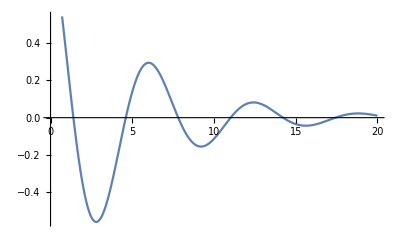

```mathematica
Plot[-Au*Exp[-βu*t]*(βu*Cos[w1u*t-π/2]+w1u*Sin[w1u*t-π/2]),{t,0,20}]
```

### Diagrama de Fase

```mathematica
u[t_]:=w1u*Au*Exp[-βu*t]*Cos[w1u*t-π/2]
v[t_]:=-w1u*Au*Exp[-βu*t]*Sin[w1u*t-π/2]
```

```mathematica
(* Varias condiciones iniciales *)
```

```mathematica
up[t_,A_]:=w1u*A*Exp[-βu*t]*Cos[w1u*t-π/2]
vp[t_,A_]:=-w1u*A*Exp[-βu*t]*Sin[w1u*t-π/2]
```

```mathematica
uvp=up[t,#]&/@{1,1.2,1.5,1.8}
vvp=vp[t,#]&/@{1,1.2,1.5,1.8}
```

{0.979796 ⅇ^(-0.2 t) Sin[0.979796 t],1.17576 ⅇ^(-0.2 t) Sin[0.979796 t],1.46969 ⅇ^(-0.2 t) Sin[0.979796 t],1.76363 ⅇ^(-0.2 t) Sin[0.979796 t]}

{0.979796 ⅇ^(-0.2 t) Cos[0.979796 t],1.17576 ⅇ^(-0.2 t) Cos[0.979796 t],1.46969 ⅇ^(-0.2 t) Cos[0.979796 t],1.76363 ⅇ^(-0.2 t) Cos[0.979796 t]}

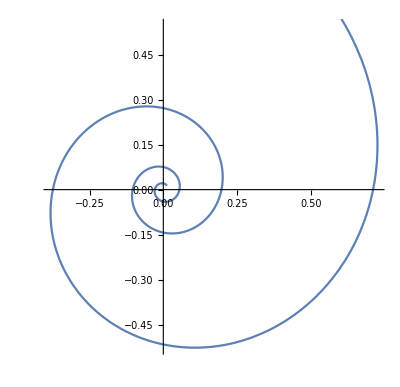

```mathematica
ParametricPlot[{u[t],v[t]},{t,0,20}]
```

```mathematica
ParametricPlot[{{uvp[[1]],vvp[[1]]},{uvp[[2]],vvp[[2]]},{uvp[[3]],vvp[[3]]},{uvp[[4]],vvp[[4]]}},{t,0,30},PlotLabels->{"A=1","A=1.2","A=1.5","A=1.8"}]
```

-Graphics-

## Amortiguamiento Crítico

```mathematica
sol=DSolve[{x''[t]+8*x'[t]+16*x[t]==0,x[0]==-1,x'[0]==8},x[t],t]
```

{{x[t]→ⅇ^(-4 t) (-1+4 t)}}

```mathematica
{{x[t]->ⅇ^(-4 t) (-1+4 t)}}
```

{{x[t]→ⅇ^(-4 t) (-1+4 t)}}

```mathematica
Xc[t_]:=x[t]/.sol
```

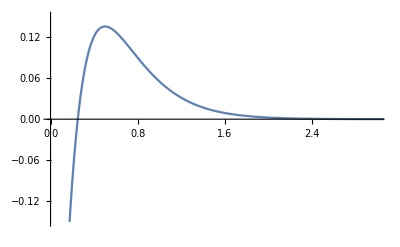

```mathematica
Plot[Xc[t],{t,0,20},PlotRange->{{0,3},{-0.15,0.15}}]
```

## Movimiento Sobreamortiguado

```mathematica
solOv=DSolve[{y''[t]+10*y'[t]+16*y[t]==0,y[0]==1,y'[0]==0},y[t],t]
```

{{y[t]→1/3 ⅇ^(-8 t) (-1+4 ⅇ^(6 t))}}

```mathematica
Xo[t_]:=y[t]/.solOv
```

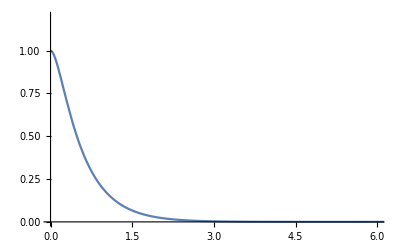

```mathematica
Plot[Xo[t],{t,0,20},PlotRange->{{0,6},{0,1.2}}]
```

## Comparando Movimientos Amortiguados

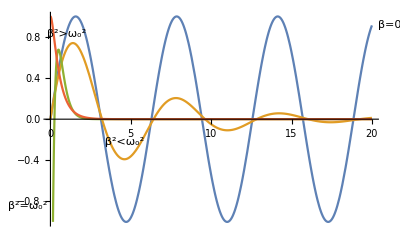

```mathematica
Plot[{Cos[t-π/2],Xu[t],5*Xc[t],Xo[t]},{t,0,20},PlotRange->{{0,20},{-1,1}},PlotLabels->Placed[{"β=0","β^2<ω_o^2","β^2=ω_o^2","β^2>ω_o^2"},{After,Bottom,Before,Top}],Ticks->None]
```